# BW transition

## Boundary states

```mathematica
$Assumptions=α>0
```

α>0

```mathematica
j0 = Subscript[j,0];
jpm = Subscript[j,pm];
```

```mathematica
σ0 = j0^(-α);
η0 = j0^(α+1) + j0^(α)/2;
σpm = jpm^(-α);
ηpm = jpm^(α+1) + jpm^(α)/2;
```

### Gaussian factor(s)

#### First case

```mathematica
Clear[j0];
Clear[α];
j0=2;
K0 =0.5;
α = 4;
```

```mathematica
j=j0 + 1;
```

```mathematica
G0 = Exp[-((j0 ^α)/2)*(j-j0)^2] // N
```

0.000335463

```mathematica
<<MaTeX`
```

```mathematica
MaTeX["G (j, j_m = 2, \alpha = 4)"]
```

-Graphics-

```mathematica
Clear[j];
G0 = Exp[-((j0 ^α)/2)*(j-j0)^2];
```

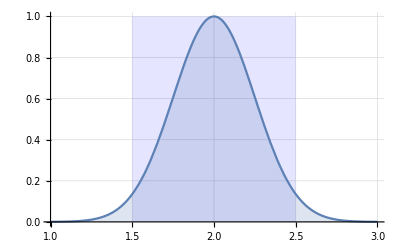

```mathematica
Plot[G0,{j,j0-1,j0+1},Prolog->{Opacity[0.1, Blue],Rectangle[{j0-K0,1}, {j0+K0,0}]},AxesLabel->{MaTeX["j"],None}, PlotLabel->-Graphics-,Filling->Axis, GridLines->Automatic]
```

```mathematica
Export["C:\\Users\\asus\\Desktop\\Gaussian_factor_jm_2_alpha_4.pdf",%400,"PDF"]
```

C:\Users\asus\Desktop\Gaussian_factor_jm_2_alpha_4.pdf

#### Second case

```mathematica
Clear[j0];
Clear[α];
j0=2.5;
K0 =0.5;
α = 4;
```

```mathematica
j=j0 + 1;
```

```mathematica
G0 = Exp[-((j0 ^α)/2)*(j-j0)^2] // N
```

3.29371×10^-9

```mathematica
MaTeX["G (j, j_m = 2.5, \alpha = 4)"]
```

-Graphics-

```mathematica
Clear[j];
G0 = Exp[-((j0 ^α)/2)*(j-j0)^2];
```

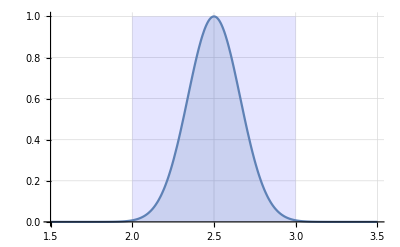

```mathematica
Plot[G0,{j,j0-1,j0+1},Prolog->{Opacity[0.1, Blue],Rectangle[{j0-K0,1}, {j0+K0,0}]},AxesLabel->{MaTeX["j"],None}, PlotLabel->-Graphics-,Filling->Axis, GridLines->Automatic]
```

```mathematica
Export["C:\\Users\\asus\\Desktop\\Gaussian_factor_jm_2.5_alpha_4.pdf",%426,"PDF"]
```

C:\Users\asus\Desktop\Gaussian_factor_jm_2.5_alpha_4.pdf

### Measure coefficient(s)

```mathematica
α = 2;
j0=7;
```

```mathematica
μ0 = (σ0/Pi)^(3/2)(Exp[-1/(4 σ0)])/(4 Pi)^2 η0 Sinh[η0] Exp[-σ0 *η0^2] // Simplify
```

(25 Sinh[1800])/(384 ⅇ^22536 π^(7/2))

```mathematica
TeXForm[μ0];
```

```mathematica
μpm = (σpm/Pi)^(3/2)(Exp[-1/(4 σpm)])/(4 Pi)^2 ηpm Sinh[ηpm] Exp[-σpm *ηpm^2]// Simplify
```

(ⅇ^(-j_pm^4 (1+j_pm)^2) (-1+ⅇ^(j_pm^4+2 j_pm^5)) √(1/j_pm^4) (1+2 j_pm))/(64 π^(7/2))

```mathematica
TeXForm[μpm ];
```

```mathematica
μ = (μ0)^4*(μpm)^12
```

(ⅇ^(-4 j_0^4 (1+j_0)^2-12 j_pm^4 (1+j_pm)^2) (-1+ⅇ^(j_0^4+2 j_0^5))^4 (-1+ⅇ^(j_pm^4+2 j_pm^5))^12 (1+2 j_0)^4 (1+2 j_pm)^12)/(79228162514264337593543950336 π^56 j_0^8 j_pm^24)

```mathematica
α = 4;
m = 1.122;
γ = 1;
```

```mathematica
Plot[μ,{T, 1, 4}]
```

-Graphics-

## Relations between m,T and boundary

```mathematica
Clear[j0];
Clear[jpm];
j0 = m^2(1 + Exp[-T/2m])^2/(2 γ);
jpm =j0/Sqrt[6] ;
ζ0 = T/(2m);
ζp = -32/9*Sqrt[6];
ζm = 32/9*Sqrt[6];
```

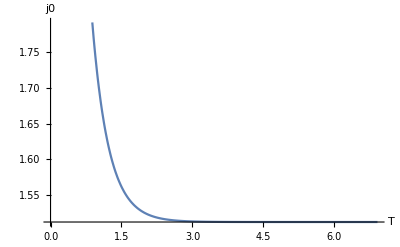

```mathematica
m = 5.5;
γ = 10;
Plot[j0,{T,0,4*Pi*m/γ}, AxesLabel->{"T","j0"}]
```

## Normal orientation